## Real points on the boundary of K_L

```mathematica
numVar=6;
numTrials=1000;
listCoef=RandomInteger[1000,{numTrials,numVar}];
```

```mathematica
K={{l1,l4,0,l4},{l4,l2,l5,0},{0,l5,l3,l6},{l4,0,l6,l2}};
```

```mathematica
L={l1,l2,l3,l4,l5,l6};
```

```mathematica
estRank={};
solL={};
For[i=1,i<numTrials+1,i++,sol=SemidefiniteOptimization[listCoef[[i]].L,{K(\[VectorGreaterEqual])_Length[K] 0,Tr[K]==1},L];
AppendTo[solL,sol];
estK=K/.sol;estRankK=MatrixRank[N[estK],Tolerance->10^(-10)];AppendTo[estRank,estRankK]]
Counts[estRank]
```

<|4→954,3→45,2→1|>

```mathematica
SemidefiniteOptimization[{-10,0,0,0,0,0}.L,{K(\[VectorGreaterEqual])_Length[K] 0,Tr[K]==1},L]
```

{l1→1.,l2→-4.03799×10^-9,l3→-4.03799×10^-9,l4→0.,l5→0.,l6→0.}

```mathematica
SemidefiniteOptimization[{0,0,-10,0,0,0}.L,{K(\[VectorGreaterEqual])_Length[K] 0,Tr[K]==1},L]
```

{l1→-1.84969×10^-9,l2→-1.84969×10^-9,l3→1.,l4→0.,l5→0.,l6→0.}

```mathematica
listCoef[[1]]
```

{803,161,98,158,819,992}

```mathematica
minPrime0={l5-l6,l2,l3 l4^2+l1 l6^2};
minPrime1={l5+l6,l2 l3 - 2 l6^2, l1 l2 -2 l4^2};
minPrime2={l4,l2,l1};
minPrime3= {l4,l1,l2 l3-l5^2-l6^2};
```

```mathematica
isZeroOfminPrime0L={};
For[i=1,i<numTrials+1,i++,isZeroOfminPrime0=Chop[minPrime0/.solL[[i]]]=={0,0,0};
AppendTo[isZeroOfminPrime0L,isZeroOfminPrime0]]
Counts[isZeroOfminPrime0L]
```

<|False→1000|>

```mathematica
isZeroOfminPrime1L={};
For[i=1,i<numTrials+1,i++,isZeroOfminPrime1=Chop[minPrime1/.solL[[i]]]=={0,0,0};
AppendTo[isZeroOfminPrime1L,isZeroOfminPrime1]]
Counts[isZeroOfminPrime1L]
```

<|False→988,True→12|>

```mathematica
isZeroOfminPrime2L={};
For[i=1,i<numTrials+1,i++,isZeroOfminPrime2=Chop[minPrime2/.solL[[i]]]=={0,0,0};
AppendTo[isZeroOfminPrime2L,isZeroOfminPrime2]]
Counts[isZeroOfminPrime2L]
```

<|False→1000|>

```mathematica
isZeroOfminPrime3L={};
For[i=1,i<numTrials+1,i++,isZeroOfminPrime3=Chop[minPrime3/.solL[[i]]]=={0,0,0};
AppendTo[isZeroOfminPrime3L,isZeroOfminPrime3]]
Counts[isZeroOfminPrime3L]
```

<|False→985,True→15|>

```mathematica
isZeroOfminPrime2L[[3]]
```

False

```mathematica
isZeroOfAnyL={};
For[i=1,i<numTrials+1,i++,isZeroOfAny=isZeroOfminPrime0L[[i]]∨ isZeroOfminPrime1L[[i]]∨isZeroOfminPrime2L[[i]]∨isZeroOfminPrime3L[[i]];
AppendTo[isZeroOfAnyL,isZeroOfAny]]
Counts[isZeroOfAnyL]
```

<|False→973,True→27|>

```mathematica
isZeroOfAnyL[[1]]
```

False

```mathematica
Position[estRank,3]
```

{{10},{11},{103},{165},{202},{398},{456},{478},{490},{494},{724},{732},{752},{795},{867},{981}}

```mathematica
Position[isZeroOfAnyL,True]
```

{{50},{64},{92},{122},{169},{227},{247},{277},{287},{347},{374},{417},{448},{482},{502},{561},{654},{688},{719},{727},{770},{804},{849},{861},{939},{944},{965}}

## Plots

```mathematica
pts={{11.7023,59.5019,37.4582,63.8209,75.6061,38.5768},{80.879,40.1886,.587323,128.433,13.8035,-2.85901},{47.9718,49.3759,18.1267,97.697,43.2029,16.8519}}
```

{{11.7023,59.5019,37.4582,63.8209,75.6061,38.5768},{80.879,40.1886,0.587323,128.433,13.8035,-2.85901},{47.9718,49.3759,18.1267,97.697,43.2029,16.8519}}

```mathematica
Subscript[f, 1][t1_,t2_,t3_,t4_,t5_,t6_]:=t1
```

```mathematica
Subscript[f, 2][t1_,t2_,t3_,t4_,t5_,t6_]:=t3
```

```mathematica
Subscript[f, 3][t1_,t2_,t3_,t4_,t5_,t6_]:=4*t2*t3-t5^2-t6^2
```

```mathematica
Subscript[f, 4][t1_,t2_,t3_,t4_,t5_,t6_]:=t3*t4^2-t1*t5^2-2*t1*t5*t6-t1*t6^2
```

```mathematica
Subscript[f, 5][t1_,t2_,t3_,t4_,t5_,t6_]:=8*t1*t2*t3-t3*t4^2-t1*t5^2+2*t1*t5*t6-t1*t6^2
```

```mathematica
ptInd={3};
coordInd={3,5,6};
```

```mathematica
ptToEvaluate=pts[[ptInd,coordInd]]
```

{{18.1267,43.2029,16.8519}}

```mathematica
subRules=Thread[coordInd->#]&/@ptToEvaluate
```

{{3→18.1267,5→43.2029,6→16.8519}}

```mathematica
restrictToPts=ReplacePart[subRules[[1]]][{t1,t2,t3,t4,t5,t6}]
```

{t1,t2,18.1267,t4,43.2029,16.8519}

```mathematica
Apply[Subscript[f, 3],restrictToPts]
```

-2150.48+72.5068 t2

```mathematica
Subscript[f, 3][47.9718,49.3759,18.1267,0,t5,t6]
```

3580.09-t5^2-t6^2

```mathematica
flist={Subscript[f, 1],Subscript[f, 2],Subscript[f, 3],Subscript[f, 4],Subscript[f, 5]}
```

{f_1,f_2,f_3,f_4,f_5}

```mathematica
restrictedFList={};
```

```mathematica
For[i=1,i<Length[flist]+1,i++,AppendTo[restrictedFList,Apply[flist[[i]],restrictToPts]]]
```

```mathematica
Plot3=ContourPlot3D[restrictedFList[[3]]==0,{t1,-200,200},{t2,-200,200},{t4,-200,200},ContourStyle->Red]
```

-Graphics3D-

```mathematica
Plot4=ContourPlot3D[restrictedFList[[4]]==0,{t1,-200,200},{t2,-200,200},{t4,-200,200}]
```

-Graphics3D-

```mathematica
Plot5=ContourPlot3D[restrictedFList[[5]]==0,{t1,-200,200},{t2,-200,200},{t4,-200,200},ContourStyle->Blue]
```

-Graphics3D-

```mathematica
Show[Plot3,Plot4,Plot5]
```

-Graphics3D-

```mathematica
Reg4=RegionPlot3D[restrictedFList[[4]]>=0,{t1,-200,200},{t2,-200,200},{t4,-200,200}, PlotStyle->Directive[Orange,Opacity[0.5]]]
```

-Graphics3D-

```mathematica
Reg5=RegionPlot3D[restrictedFList[[5]]>=0,{t1,-200,200},{t2,-200,200},{t4,-200,200}, PlotStyle->Directive[Blue,Opacity[0.5]]]
```

-Graphics3D-

```mathematica
Reg45=RegionPlot3D[restrictedFList[[4]]>=0 && restrictedFList[[5]]>=0,{t1,-200,200},{t2,-200,200},{t4,-200,200}]
```

-Graphics3D-

```mathematica
Show[Plot3, Reg4,Reg5]
```

-Graphics3D-

```mathematica
RegionPlot3D[{restrictedFList[[4]]>=0 && restrictedFList[[5]]>=0&&restrictedFList[[3]]>=0},{t1,-200,200},{t2,-200,200},{t4,-200,200}]
```

-Graphics3D-

```mathematica
P45=RegionPlot3D[{restrictedFList[[1]]>=0 &&restrictedFList[[4]]>=0 && restrictedFList[[5]]>=0},{t1,-200,200},{t2,-200,200},{t4,-200,200}]
```

-Graphics3D-

```mathematica
P34=RegionPlot3D[{restrictedFList[[1]]>=0 &&restrictedFList[[3]]<=0 && restrictedFList[[4]]>=0},{t1,-200,200},{t2,-200,200},{t4,-200,200}]
```

-Graphics3D-

```mathematica
P35=RegionPlot3D[{restrictedFList[[1]]>=0 &&restrictedFList[[3]]<=0 && restrictedFList[[5]]>=0},{t1,-200,200},{t2,-200,200},{t4,-200,200}]
```

-Graphics3D-

```mathematica
Show[P35,P45]
```

-Graphics3D-

```mathematica
Show[P45,P35]
```

-Graphics3D-

```mathematica
Show[Plot3,Plot4,Plot5]
```

-Graphics3D-

```mathematica
Show[Plot3, Reg4,Reg5]
```

-Graphics3D-

```mathematica
Show[Plot3, Reg5]
```

-Graphics3D-

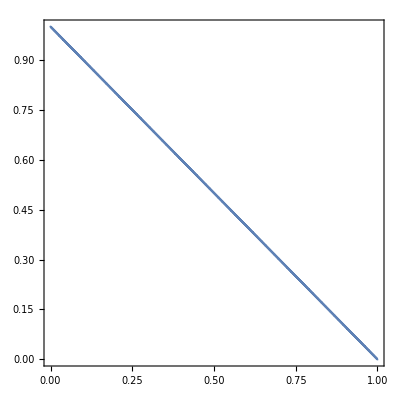

```mathematica
RegionPlot[x+y==1 && x y>=0, {x,0,1},{y,0,1}]
```